## Compare Entropy Functions

See Coupled Functions file for the CoupledEntropy Function.
The Tsallis and Normalized Tsallis entropy functions are related to the non-root form of the Coupled Entropy
	TsallisNormalizedEntropy = (1 + κ) CoupledEntropy
	TsallisEntropy = (1 + κ) Sum(p_i^(1+(α κ)/(1+κ)))CoupledEntropy

```mathematica
TsallisEntropy[dist_,κ_,α_:1,d_:1,limits_:{-∞,∞},normalize_:False]:=
If[normalize,
(1+κ)CoupledEntropy[dist,κ,α,d,limits,False],
(1+κ)CoupledEntropy[dist,κ,α,d,limits,False]∫_limits⟦1⟧^limits⟦2⟧ PDF[dist,x]^(1+α κ/(1+κ))ⅆx 
];

TsallisRootEntropy[dist_,κ_,α_:1,d_:1,limits_:{-∞,∞},normalize_:False]:=
If[normalize,
(1+κ)CoupledEntropy[dist,κ,α,d,limits,True],
(1+κ)CoupledEntropy[dist,κ,α,d,limits,True]∫_limits⟦1⟧^limits⟦2⟧ PDF[dist,x]^(1+α κ/(1+κ))ⅆx 
]
```

#### Plot Comparison

Compare entropies when the coupling matches the distribution

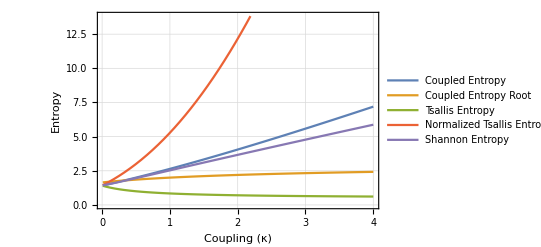

```mathematica
PlotCoupledEntDist[2]
```

```mathematica
PlotCoupledEntDist[α_]:=
Module[{coupledDist},
coupledDist=CoupledNormalDistribution[0.,1.,κ];
Plot[
{
CoupledEntropy[coupledDist,κ,α,1,{-∞,∞},False],
CoupledEntropy[coupledDist,κ,α,1,{-∞,∞},True],
TsallisEntropy[coupledDist,κ,α,1,{-∞,∞},False],
TsallisEntropy[coupledDist,κ,α,1,{-∞,∞},True],
CoupledEntropy[coupledDist,0,1,1,{-∞,∞},False]
},{κ,0.01,4},
PlotLegends->{"Coupled Entropy", "Coupled Entropy Root", 
"Tsallis Entropy", "Normalized Tsallis Entropy", "Shannon Entropy"},
PlotTheme->"Detailed",
FrameLabel->{"Coupling (κ)", "Entropy"}
]
]
```

Plot with all entropies taking root

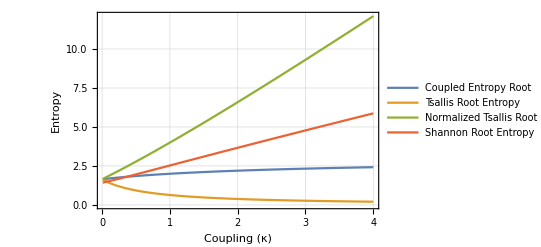

```mathematica
PlotCoupledEntDist[2]
```

```mathematica
PlotCoupledEntDist[α_]:=
Module[{coupledDist},
coupledDist=CoupledNormalDistribution[0.,1.,κ];
Plot[
{
CoupledEntropy[coupledDist,κ,α,1,{-∞,∞},True],
TsallisRootEntropy[coupledDist,κ,α,1,{-∞,∞},False],
TsallisRootEntropy[coupledDist,κ,α,1,{-∞,∞},True],
CoupledEntropy[coupledDist,0,1,1,{-∞,∞},True]
},{κ,0.01,4},
PlotLegends->{"Coupled Entropy Root", "Tsallis Root Entropy", "Normalized Tsallis Root Entropy", "Shannon Root Entropy"},
PlotTheme->"Detailed",
FrameLabel->{"Coupling (κ)", "Entropy"}
]
]
```

Compare Entropies for a Cauchy Distribution

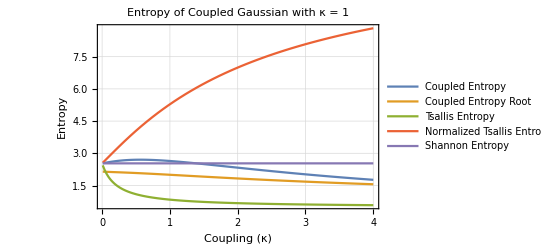

```mathematica
PlotCoupledEntDist[2,1]
```

```mathematica
PlotCoupledEntDist[α_,κDist_]:=
Module[{coupledDist},
coupledDist=CoupledNormalDistribution[0.,1.,κDist];
Plot[
{
CoupledEntropy[coupledDist,κ,α,1,{-∞,∞},False],
CoupledEntropy[coupledDist,κ,α,1,{-∞,∞},True],
TsallisEntropy[coupledDist,κ,α,1,{-∞,∞},False],
TsallisEntropy[coupledDist,κ,α,1,{-∞,∞},True],
CoupledEntropy[coupledDist,0,1,1,{-∞,∞},False]
},{κ,0.01,4},
PlotLegends->{"Coupled Entropy", "Coupled Entropy Root", 
"Tsallis Entropy", "Normalized Tsallis Entropy", "Shannon Entropy"},
PlotTheme->"Detailed",
FrameLabel->{"Coupling (κ)", "Entropy"},
PlotLabel->"Entropy of Coupled Gaussian with κ = "<>ToString[κDist]
]
]
```

Comparison when other entropies also have a root term

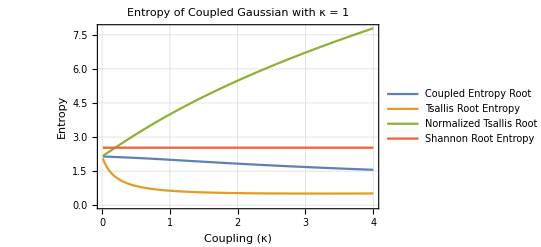

```mathematica
PlotCoupledEntDist[2,1]
```

```mathematica
PlotCoupledEntDist[α_,κDist_]:=
Module[{coupledDist},
coupledDist=CoupledNormalDistribution[0.,1.,κDist];
Plot[
{
CoupledEntropy[coupledDist,κ,α,1,{-∞,∞},True],
TsallisRootEntropy[coupledDist,κ,α,1,{-∞,∞},False],
TsallisRootEntropy[coupledDist,κ,α,1,{-∞,∞},True],
CoupledEntropy[coupledDist,0,1,1,{-∞,∞},True]
},{κ,0.01,4},
PlotLegends->{ "Coupled Entropy Root", "Tsallis Root Entropy", "Normalized Tsallis Root Entropy", "Shannon Root Entropy"},
PlotTheme->"Detailed",
FrameLabel->{"Coupling (κ)", "Entropy"},
PlotLabel->"Entropy of Coupled Gaussian with κ = "<>ToString[κDist]
]
]
```

Derivative as a function of coupling for the Coupled Entropy, Coupled Root Entropy, and Tsallis Entropy

```mathematica
PlotDerivativeCoupledEntDist[2,1]
```

General::ivar: 0.0100815 is not a valid variable.

General::ivar: 0.0915101 is not a valid variable.

General::ivar: 0.172939 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

$Aborted

```mathematica
PlotDerivativeCoupledEntDist[α_,κDist_]:=
Module[{coupledDist},
coupledDist=CoupledNormalDistribution[0.,1.,κDist];
Plot[
DifferenceQuotient[
{
CoupledEntropy[coupledDist,κ,α,1,{-∞,∞},False],
(*CoupledEntropy[coupledDist,κ,α,1,{-∞,∞},True],*)
TsallisEntropy[coupledDist,κ,α,1,{-∞,∞},False],
TsallisEntropy[coupledDist,κ,α,1,{-∞,∞},True],
CoupledEntropy[coupledDist,0,1,1,{-∞,∞},False]
},
{κ,0.01}],
{κ,0.01,4},
PlotLegends->{"Coupled Entropy", "Coupled Entropy Root", 
"Tsallis Entropy", "Normalized Tsallis Entropy", "Shannon Entropy"},
PlotTheme->"Detailed",
FrameLabel->{"Coupling (κ)", "Entropy"},
PlotLabel->"Derivative of Entropy of Coupled Gaussian with κ = "<>ToString[κDist]
]
]
```

#### Limit of Coupled Root Entropy

Need symbolic definition of Coupled Root Entropy

```mathematica
Limit[CoupledEntropy[CoupledNormalDistribution[0.,σ,κ],κ,2,1,{-∞,∞},True],
κ->∞]
```

NIntegrate::inumr: The integrand If[κ==0,PDF[ProbabilityDistribution[1/(Piecewise[{«2»},Times[«5»]] √Which[Greater[«2»],«6»,Message[«2»]]),If[κ≥0,{x$13681176,-DirectedInfinity[«1»],∞},{x$13681176,0.+Times[«2»],0.+√(«1»)}]],x],FullSimplify[PDF[ProbabilityDistribution[Times[«2»],If[«3»]],x]^(1-Times[«3»])/(∫_DirectedInfinity[«1»]^DirectedInfinity[«1»] PDF[«2»]^Plus[«2»]ⅆy)]] √If[«1»] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0.}}.

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

$Aborted

#### Test functionality of CoupledEntropy

```mathematica
$Assumptions=-1<κ<∞&&0<σ<∞&&{x,κ,σ}∈Reals;
```

```mathematica
CoupledEntropy[CoupledNormalDistribution[0,1,1],κ,2]
```

$Aborted

```mathematica
CoupledEntropy[CoupledNormalDistribution[0,1,1],#,2]&/@{-0.5,0.,0.5,1.,1.5}
```

Integrate::idiv: Integral of 3.14159 (1+y^2)^1. does not converge on {-∞,∞}.

{-∫_(-∞)^∞ -((1.5708 ((1+x^2)^2)^0.5 If[(1+x^2)^2≥0,If[-0.5≠0,-((π^2 (1+x^2)^2)^(-0.5/(1+1 (-0.5)))-1)/0.5,Log[π^2 (1+x^2)^2]],Undefined])/(∫_(-∞)^∞ 3.14159 ((1+y^2)^2)^0.5ⅆy))ⅆx,2.53102,2.69962,2.64159,2.4964}

```mathematica
CoupledEntropy[CoupledNormalDistribution[0,1,0.5],#,2]&/@{0.,0.5,1.,1.5}
```

{1.96028,2.,1.90084,1.76309}

```mathematica
CoupledEntropy[CoupledNormalDistribution[0,1,1.5],#,2]&/@{0.,0.5,1.,1.5}
```

{3.10166,3.45102,3.46597,3.32999}

#### Test functionality of CoupledEntropy with Root

```mathematica
CoupledEntropy[CoupledNormalDistribution[0,1,1],#,2,1,{-∞,∞},True]&/@{0.,0.5,1.,1.5}
```

{2.1464,2.08107,1.99952,1.91187}

```mathematica
CoupledEntropy[CoupledNormalDistribution[0,1,0.5],#,2,1,{-∞,∞},True]&/@{0.,0.5,1.,1.5}
```

{1.90805,1.85407,1.77247,1.68738}

```mathematica
CoupledEntropy[CoupledNormalDistribution[0,1,1.5],#,2,1,{-∞,∞},True]&/@{0.,0.5,1.,1.5}
```

{2.35969,2.27791,2.19773,2.10942}

```mathematica
?CoupledEntropy
```